```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["EccentricPN.m"]
```

## Definitions

```mathematica
etaOfq[q_]:=q/(1+q)^2
```

## Binary Parameters

```mathematica
idParams={e->0.00001,q->3,n->0.0145,eta->etaOfq[q],u->Pi }
```

{e→0.00001,q→3,n→0.0145,eta→q/(1+q)^2,u→π}

## Compute linear momentum for initial data

```mathematica
val1 = {e->0.00001,q->3,n->0.0145,eta->0.187,u->π};
xid = n/.val1;
```

```mathematica
xid
```

0.0145

```mathematica
nInxe = SeriesData[x, 0, {1, 0, 3/(-1 + e^2), 0, (-18 + 28*eta + e^2*(-51 + 26*eta))/
   (4*(-1 + e^2)^2), 0, 
  -(16*e^4*(-156 + 240/Sqrt[1 - e^2] + (110 - 96/Sqrt[1 - e^2])*eta - 
       65*eta^2) + 4*(48 - 480/Sqrt[1 - e^2] - 224*eta^2 + 
       eta*(3656 + 192/Sqrt[1 - e^2] - 123*Pi^2)) + 
     e^2*(96*(-89 - 20/Sqrt[1 - e^2]) - 5120*eta^2 + 
       eta*(17856 + 768/Sqrt[1 - e^2] - 123*Pi^2)))/(128*(-1 + e^2)^3)}, 3, 
 11, 2];
rInxe = SeriesData[x,0,{1-e*Cos[u],0,(2*(-1+e*Cos[u]))/(-1+e^2)+(2*(-9+eta)+e*(-6+7*eta)*Cos[u])/6,0,((-48+28*eta+e^2*(-51+26*eta))*(-1+e*Cos[u]))/(6*(-1+e^2)^2)+(72*(-4+7*eta)+36*Sqrt[1-e^2]*(-5+2*eta)*(2+e*Cos[u])+(1-e^2)*(72+30*eta+8*eta^2-e*(72-231*eta+35*eta^2)*Cos[u]))/(72*(1-e^2)),0,-((16*e^4*(-240+156*Sqrt[1-e^2]+(96-110*Sqrt[1-e^2])*eta+65*Sqrt[1-e^2]*eta^2)+4*(32*(15+41*Sqrt[1-e^2])+224*Sqrt[1-e^2]*eta^2+3*eta*(-64-1592*Sqrt[1-e^2]+41*Sqrt[1-e^2]*Pi^2))+e^2*(192*(10+87*Sqrt[1-e^2])+5120*Sqrt[1-e^2]*eta^2+eta*(-256*(3+86*Sqrt[1-e^2])+123*Sqrt[1-e^2]*Pi^2)))*(-1+e*Cos[u]))/(192*(1-e^2)^(7/2))-(72*(-4+7*eta)+36*Sqrt[1-e^2]*(-5+2*eta)*(2+e*Cos[u])+(1-e^2)*(72+30*eta+8*eta^2-e*(72-231*eta+35*eta^2)*Cos[u]))/(36*(-1+e^2)^2)+(-70/3+(56221*eta)/840-(151*eta^2)/36+(2*eta^3)/81-(123*eta*Pi^2)/64+(e*(-864+7047*eta-3933*eta^2+49*eta^3)*Cos[u])/1296+e^2*(-52/3-(341*eta^2)/18-(4*eta^3)/81+eta*(2099/35-(41*Pi^2)/64)-(e*(-864+7047*eta-3933*eta^2+49*eta^3)*Cos[u])/648)+(e^4*(2*(432-81*eta+90*eta^2+16*eta^3)+e*(-864+7047*eta-3933*eta^2+49*eta^3)*Cos[u]))/1296+(Sqrt[1-e^2]*(-2*(8640-13184*eta+960*eta^2+96*e^2*(30-29*eta+11*eta^2)+123*eta*Pi^2)+e*(-12960+19952*eta-2976*eta^2+48*e^2*(30-83*eta+20*eta^2)-123*eta*Pi^2)*Cos[u]))/576)/(-1+e^2)^2},-2,6,2];
jInxe = SeriesData[x,0,{1-e^2,0,(9+eta+e^2*(-17+7*eta))/4,0,(-81+57*eta-eta^2+e^4*(-225+277*eta-29*eta^2)+e^2*(18+360*Sqrt[1-e^2]+(98-144*Sqrt[1-e^2])*eta+30*eta^2))/(24*(-1+e^2)),0,(35*e^4*(15*(219+704*Sqrt[1-e^2])-3*(3437+2560*Sqrt[1-e^2])*eta+(6682+576*Sqrt[1-e^2])*eta^2-131*eta^3)+35*e^6*(-2271+7381*eta-2414*eta^2+65*eta^3)-35*(27*(83-80*Sqrt[1-e^2])+(-334+96*Sqrt[1-e^2])*eta^2+eta^3+eta*(5797+624*Sqrt[1-e^2]-246*Pi^2))+e^2*(533505-848400*Sqrt[1-e^2]-210*(-1281+752*Sqrt[1-e^2])*eta^2+2345*eta^3+eta*(-1311067+1247120*Sqrt[1-e^2]-8610*(-3+Sqrt[1-e^2])*Pi^2)))/(6720*(-1+e^2)^2)},0,8,2];
```

```mathematica
EpsInxe = SeriesData[x,0,{1,0,5/4+2/(-1+e^2)-eta/12,0,5/8+5/Sqrt[1-e^2]+(-1+e^2)^(-2)-(-15+eta)/(3*(-1+e^2))-(5*eta)/8-(2*eta)/Sqrt[1-e^2]-eta^2/24+(-30+28*eta+e^2*(-51+26*eta))/(6*(-1+e^2)^2),0,-(405*(-32+167*Sqrt[1-e^2])+54*(-352+507*Sqrt[1-e^2])*eta^2+35*Sqrt[1-e^2]*eta^3-e^6*(135*(-96+37*Sqrt[1-e^2])+27*(-736+225*Sqrt[1-e^2])*eta+90*(192+5*Sqrt[1-e^2])*eta^2+35*Sqrt[1-e^2]*eta^3)+9*eta*(20512-54957*Sqrt[1-e^2]+246*(-1+6*Sqrt[1-e^2])*Pi^2)+3*e^4*(-27*(2400+103*Sqrt[1-e^2])+6*(864+1355*Sqrt[1-e^2])*eta^2+35*Sqrt[1-e^2]*eta^3+eta*(69024+4923*Sqrt[1-e^2]-738*Pi^2))+3*e^2*(27*(2400+3767*Sqrt[1-e^2])+6*(1152+7733*Sqrt[1-e^2])*eta^2-35*Sqrt[1-e^2]*eta^3+3*eta*(-45728-53913*Sqrt[1-e^2]+123*(4+3*Sqrt[1-e^2])*Pi^2)))/(5184*(1-e^2)^(7/2))},2,10,2];
```

```mathematica
xv = Normal[InverseSeries[nInxe]/.val1 ]/.{x-> xid};
```

```mathematica
x0 = Normal[rInxe]/2/.{x-> xv}//.val1;
Py = eta Sqrt[Normal[jInxe]/Normal[EpsInxe]]/Normal[rInxe]/.val1//.{x-> xv};
```

```mathematica
Py
```

0.0548096

```mathematica
x0
```

8.4381

```mathematica
twoPuncturesParams[x0_,Py_]:=
StringJoin[Riffle[
{"TwoPunctures::par_b = "<>ToString[x0,CForm],
"TwoPunctures::par_p_plus[1] = "<>ToString[Py,CForm],
"TwoPunctures::par_p_minus[1] = "<>ToString[-Py,CForm]},"\n"]]
```

```mathematica
twoPuncturesParams[x0,Py]
```

TwoPunctures::par_b = 6.741713597216806
TwoPunctures::par_p_plus[1] = 0.06995813079831047
TwoPunctures::par_p_minus[1] = -0.06995813079831047

## Inspiral

```mathematica
xInne = Normal[InverseSeries[nInxe]/.val1 ]/.{x-> xid};
```

```mathematica
genSoln[id_,tMax_]:=
EccentricSoln[xeModel,eta//.id,{Normal[xInne]//.id,e//.id,Pi//N,0},0,{0,tMax,1}]
```

```mathematica
tMax=4000;
```

```mathematica
soln=genSoln[idParams,tMax]
```

{EccentricIMR`EccentricPNSymbols`r→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`om→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`phi→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`x→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`e→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`u→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`l→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`h→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`hPhi→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`psi4→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`psi4Om→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`psi4Phi→InterpolatingFunction[…],EccentricIMR`EccentricPNSymbols`hOm→InterpolatingFunction[…]}

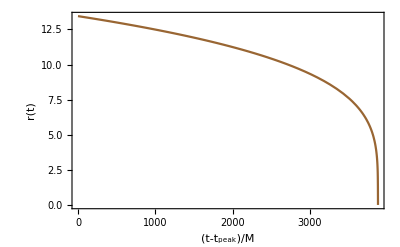

```mathematica
plotr =Plot[Evaluate[EccentricIMR`EccentricPNSymbols`r[t]/.soln],{t,0,tMax},PlotRange->{0,All},Frame->True,PlotStyle->{Brown,Thickness->0.004},FrameLabel->{(t-Subscript[t, peak])/M,r[t]},RotateLabel->False,FrameStyle->Directive[Black,14]]
```

```mathematica
Export["rplot30.eps",plotr]
```

rplot30.eps

rplot30.eps

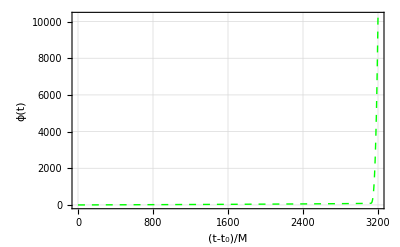

```mathematica
Plot[Evaluate[EccentricIMR`EccentricPNSymbols`phi[t]/.soln],{t,0,tMax},PlotRange->{0,All},GridLines->Automatic,Frame->True,PlotStyle->{Green,Dashed,Thick},FrameLabel->{(t-Subscript[t, 0])/M,ϕ[t]},LabelStyle->Directive[Bold, Black],FrameStyle->Directive[Black,Bold],{}]
```

```mathematica
FindRoot[Evaluate[EccentricIMR`EccentricPNSymbols`phi[t]/.soln]==4.Pi,{t,1000}]
```

{t→833.042}

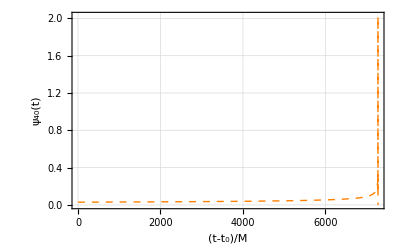

```mathematica
Plot[Evaluate[-EccentricIMR`EccentricPNSymbols`psi4Om[t]/.soln],{t,0,tMax},PlotRange->{0,All},GridLines->Automatic,Frame->True,PlotStyle->{Orange,Dashed,Thick},FrameLabel->{(t-Subscript[t, 0])/M,Subscript[ψ, 40][t]},LabelStyle->Directive[Bold, Black],FrameStyle->Directive[Black,Bold]]
```

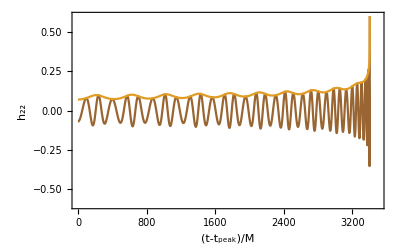

```mathematica
ploth = Plot[{Evaluate[Re@EccentricIMR`EccentricPNSymbols`h[t]/.soln],Evaluate[Abs@EccentricIMR`EccentricPNSymbols`h[t]/.soln]},{t,0,tMax},PlotRange->{-.6,0.6},Frame->True,FrameLabel->{(t-Subscript[t, peak])/M,Subscript[h, 22]},RotateLabel->False,PlotStyle-> {Brown,Thickness-> 0.004},FrameStyle->Directive[Black,14]]
```

```mathematica
Export["hplot31.eps",ploth]
```

hplot31.eps

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["hplot.eps"]]]
```

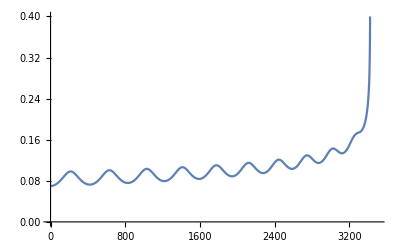

```mathematica
Plot[Evaluate[Abs@EccentricIMR`EccentricPNSymbols`h[t]/.soln],{t,0,tMax},PlotRange->{0,0.4}]
```